## Setup

This setup uses (n,η) variables instead of (ρ,η).

### PDE solver

```mathematica
ClearAll@runTwoComponentSim;
Options[runTwoComponentSim]=Join[Options[NDSolve],{"GridPoints"->200,"BC"->"Reflective"}];
runTwoComponentSim[{fhat_,uSource_,vSource_},params_,{nInit_,etaInit_},tMax_,opts:OptionsPattern[]]:=First@NDSolve[{
D[n[x,t],t]==Dv D[eta[x,t],{x,2}]
+(eps (uSource+vSource)/.{n->n[x,t],η->eta[x,t]}),D[eta[x,t],t]==Dv (1+Du/Dv) D[eta[x,t],{x,2}]-Du D[n[x,t],{x,2}]
+(-fhat+eps(Du/Dv uSource+vSource)/.{n->n[x,t],η->eta[x,t]}),
If[OptionValue["BC"]==="Periodic",
{(* periodic BCs *)
n[0,t]==n[L,t],eta[0,t]==eta[L,t],(D[n[x,t],x]/.x->0)==(D[n[x,t],x]/.x->L),(D[eta[x,t],x]/.x->0)==(D[eta[x,t],x]/.x->L)
},
{(* no-flux BCs *)
(D[n[x,t],x]/.x->0)==0,(D[eta[x,t],x]/.x->0)==0,(D[n[x,t],x]/.x->L)==0,(D[eta[x,t],x]/.x->L)==0
}
],
(* initial condition *)
n[x,0]==nInit[x],
eta[x,0]==etaInit[x]
}/.params,
{n,eta},
{x,0,L/.params},
{t,0,tMax},
Evaluate[Sequence@@FilterRules[List@opts,Options[NDSolve]]],Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->OptionValue["GridPoints"],"MaxPoints"->OptionValue["GridPoints"],AccuracyGoal->0,PrecisionGoal->0,"DifferenceOrder"->2},(*Choose higher scale factor to enforce boundary conditions in case the initial condition does not fulfil them*)"DifferentiateBoundaryConditions"->{True,"ScaleFactor"->1},"Method"->{"IDA","ImplicitSolver"->"Newton"}}
];
```

### Finite difference equations for stationary state

```mathematica
ClearAll@discreteLaplace;
discreteLaplace[data_]:=With[{paddedData=Join[{data[[1]]},data,{data[[-1]]}]},
Differences[paddedData,2]*Length[data]^2
];
```

For uniform grid with gridRes setting number of grid points.

```mathematica
ClearAll@setupFiniteDifferenceEqs;
setupFiniteDifferenceEqs[{fhat_,uSource_,vSource_},gridRes_]:=With[{
nVec=Thread[n@Range[gridRes]],
etaVec=Thread[eta@Range[gridRes]]
},
<|
"UnitGrid"->Range[1/(2*gridRes),1,1/gridRes],
"nVec"->nVec,
"etaVec"->etaVec,
"Vars"->Join[nVec,etaVec],
"Weights"->Array[1/gridRes&,gridRes],
"Eqs"->{
Dv discreteLaplace[etaVec]/L^2
+(eps(uSource+vSource)/.{n->nVec,η->etaVec}),
(Du+Dv) discreteLaplace[etaVec]/L^2
-Du discreteLaplace[nVec]/L^2
+(-fhat+eps(Du/Dv uSource+vSource)/.{n->nVec,η->etaVec})
}
|>
]
```

```mathematica
getInitGuess[fdSetup_,params_,initSol_]:=Join[
Transpose[{
fdSetup["nVec"],
n[x,T]/.params/.initSol/.x->(L/.params) fdSetup["UnitGrid"]
}],
Transpose[{
fdSetup["etaVec"],
eta[x,T]/.params/.initSol/.x->(L/.params) fdSetup["UnitGrid"]
}]
]
```

### Jacobian

```mathematica
laplaceMatrixAS[n_?NumericQ]:=SparseArray[{
{1,1}->-1,{-1,-1}->-3,
{i_,i_}->-2,
{i_,j_}/;Abs[i-j]==1->1
},
{n,n}
]*n^2;
```

```mathematica
laplaceMatrixS[n_?NumericQ]:=SparseArray[{
{1,1}->-1,{-1,-1}->-1,
{i_,i_}->-2,
{i_,j_}/;Abs[i-j]==1->1
},
{n,n}
]*n^2;
```

```mathematica
ClearAll@constructGluedJacobian;
Options@constructGluedJacobian={"Reverse"->False,"Symmetric"->False};
constructGluedJacobian[fdSetup_,params_,statSol_,dfdu_,OptionsPattern[]]:=
Block[{
solVec=If[OptionValue["Reverse"]===True,Reverse@#,#]&@Transpose[{
fdSetup["nVec"]/.statSol,
fdSetup["etaVec"]/.statSol
}],
dfduP=dfdu/.params,
gridRes=Length@fdSetup["UnitGrid"]
},
KroneckerProduct[If[OptionValue["Symmetric"]===True,laplaceMatrixS,laplaceMatrixAS][gridRes],{{0,Dv},{-Du,(Du+Dv)}}/L^2/.params]+
SparseArray[
Table[
Band[1+{2(i-1),2(i-1)}]->(dfduP/.Thread[{n,η}->solVec[[i]]]),
{i,gridRes}
]
]
];
```

### Finite-differences setup for the mass-conserving system

```mathematica
ClearAll@setupFiniteDifferenceEqsMC;
setupFiniteDifferenceEqsMC[f_,gridRes_]:=With[{
nVec=Thread[n@Range[gridRes]]
},
<|
"UnitGrid"->Range[1/(2*gridRes),1,1/gridRes],
"nVec"->nVec,
"Vars"->Join[nVec,{eta}],
"Weights"->Array[1/gridRes&,gridRes],
"Eqs"->{
Du discreteLaplace[nVec]/L^2+(f/.{n->nVec,η->eta}),
Mean@nVec- rhobar
}
|>
]
```

```mathematica
getInitGuessMC[fdSetup_,params_,initSol_,Teval_]:=Join[
Transpose[{
fdSetup["nVec"],
n[x,Teval]/.params/.initSol/.Partition[Thread[x->(L/.params) fdSetup["UnitGrid"]],1]
}],
{{eta,eta[0,Teval]/.params/.initSol}}
]
```

### Jacobian mass-conserving

Same as “normal” Jacobian but uses the stationary state differently because only one eta and not an etaVec.

```mathematica
ClearAll@constructGluedJacobianMC;
Options@constructGluedJacobianMC={"Reverse"->False,"Symmetric"->False};
constructGluedJacobianMC[fdSetup_,params_,statSol_,dfdu_,OptionsPattern[]]:=
Block[{
solVec=If[OptionValue["Reverse"]===True,Reverse@#,#]&@Transpose[{
fdSetup["nVec"]/.statSol,
Array[(eta/.statSol)&,Length@fdSetup["UnitGrid"]]
}],
dfduP=dfdu/.params,
gridRes=Length@fdSetup["UnitGrid"]
},
KroneckerProduct[If[OptionValue["Symmetric"]===True,laplaceMatrixS,laplaceMatrixAS][gridRes],{{0,Dv},{-Du,(Du+Dv)}}/L^2/.params]+
SparseArray[
Table[
Band[1+{2(i-1),2(i-1)}]->(dfduP/.Thread[{n,η}->solVec[[i]]]),
{i,gridRes}
]
]
];
```

### Analytic growth rates and thresholds

#### specific for Brusselator model

tRelax: To find the corresponding mass-conserving pattern with the correct mass, the full 2cRD dynamics is solved with the source terms, which are turned off slowly on the timescale tRelax;
deltaRhoBar: the difference in the average total density used to numerically calculate the derivatives with respect to the peak/mesa mass

```mathematica
ClearAll@analytics;
Options@analytics={"tRelax"->1000,"deltaRhoBar"->10^-3};
analytics[{f_,su_,sv_},params_,fdSetupMC_,opts:OptionsPattern[]]:=Block[
{
initRun,t0=OptionValue["tRelax"],discSol,
statSol1,statSol2,statSol3,
ρBar,ρMin,
paramsL,
peaks=False,ρfbsNc,ξL,sL,sU,
dρdρBar,dηdρBar,d2ρdρBar2,
lInt,
fη,fηρ,fηAvg,fη2Avg,fηρAvg2,
dSρdρ,dSρdρAvg,
sM,dsMdρ,sMAvg,sM2Avg,dsMdρAvg,dsMdρAvg2,
dSMdρBar,
σD,σR,σMC,σ,ϵStop
},
If[KeyExistsQ[params,Dv],
paramsL=params;,
paramsL=Join[{Dv->(10Du/.params)},params];
];

(*stat. states*)
initRun=runTwoComponentSim[
{f,su*Exp[-t/t0],sv*Exp[-t/t0]},
paramsL,
{
p*(1+0.5*Cos[Pi #/L])&,
0&
},
35*t0(*then Exp[-t/t0] < 10^-15*)
];
discSol=n[x*L,35*t0]/.paramsL/.initRun/.x->Range[0.02,1,0.04];
(*test for pattern being uniform*)
If[Variance[discSol]<1,
PrintTemporary["No pattern!"];
<|
"params"->params,
"failed"->True
|>,
statSol1=Quiet[Check[Block[{n,eta},FindRoot[
Join[fdSetupMC["Eqs"][[1]],{((su+sv)/.{n->fdSetupMC["nVec"],η->eta}).fdSetupMC["Weights"]}]/.paramsL,
getInitGuessMC[fdSetupMC,paramsL,initRun,35*t0],
AccuracyGoal->20,
PrecisionGoal->20,
WorkingPrecision->100
]
],3I,FindRoot::cvmit],FindRoot::cvmit];

If[statSol1===3I,
PrintTemporary["Not converging!"];
<|
"params"->params,
"failed"->True
|>,

ρBar=SetPrecision[fdSetupMC["Weights"].fdSetupMC["nVec"]/.statSol1,110];

(*nullcline intersections, source terms in upper/lower plateau, plateau lengths.*)
ρfbsNc=n/.Solve[0==f,n]/.η->eta/.statSol1;
If[2==Length@ρfbsNc,
peaks=True;
ξL=1;,(*length of lower plateau*)
peaks=False;
sL=Abs[su+sv/.{n->ρfbsNc[[1]],η->(eta/.statSol1)}]/.paramsL;(*total source term in lower plateau*)
sU=Abs[su+sv/.{n->ρfbsNc[[-1]],η->(eta/.statSol1)}]/.paramsL;(*total source term in upper plateau*)
ξL=sU/(sU+sL);(*length of lower plateau*)
];
ρMin=ρfbsNc[[1]]/.params;

(*We first have to see whether we need to construct the stationary pattern on a larger domain to isolate del_M^+ etastat (Appendix H)*)
If[ξL<0.6,(*then use a larger domain such that ξL=0.7*)
paramsL=Join[{L->SetPrecision[((1-ξL)*10/3*L/.paramsL),110]},DeleteCases[paramsL,L->_]];
ρBar=SetPrecision[ρMin+(ρBar-ρMin)*(L/.params)/(L/.paramsL),110];
statSol1=Block[{n,eta},FindRoot[
fdSetupMC["Eqs"]/.rhobar->ρBar/.paramsL,
getInitGuessMC[fdSetupMC,paramsL,{n->((n[Min[#,(L/.params)],35*t0]/.initRun)&),initRun[[2]]},35*t0],
AccuracyGoal->20,
PrecisionGoal->20,
WorkingPrecision->100
]
];,
paramsL=params;
];

(*stat. patterns at little higher and lower average densities to calculate discrete derivatives with respect to M*)
statSol2=Block[{n,eta},FindRoot[
fdSetupMC["Eqs"]/.rhobar->(ρBar+OptionValue["deltaRhoBar"])/.paramsL,
statSol1/.Rule->List,
AccuracyGoal->20,
PrecisionGoal->20,
WorkingPrecision->100
]
];
statSol3=Block[{n,eta},FindRoot[
fdSetupMC["Eqs"]/.rhobar->(ρBar-OptionValue["deltaRhoBar"])/.paramsL,
statSol1/.Rule->List,
AccuracyGoal->20,
PrecisionGoal->20,
WorkingPrecision->100
]
];

(*profile derivatives, central differences*)
dρdρBar=((fdSetupMC["nVec"]/.statSol2)-(fdSetupMC["nVec"]/.statSol3))/(2*OptionValue["deltaRhoBar"]);
dηdρBar=((eta/.statSol2)-(eta/.statSol3))/(2*OptionValue["deltaRhoBar"]);
d2ρdρBar2=((fdSetupMC["nVec"]/.statSol2)+(fdSetupMC["nVec"]/.statSol3)-2(fdSetupMC["nVec"]/.statSol1))/OptionValue["deltaRhoBar"]^2;

(*averages*)
lInt=L/(Total[fdSetupMC["Weights"]*dρdρBar*dρdρBar])/.paramsL;
fη=D[f,η]/.n->fdSetupMC["nVec"]/.η->eta;
fηρ=D[f,η,n]/.n->fdSetupMC["nVec"]/.η->eta;
fηAvg=Total[fdSetupMC["Weights"]*dρdρBar*fη/.statSol1]/.paramsL;
fη2Avg=Total[fdSetupMC["Weights"]*d2ρdρBar2*fη/.statSol1]/.paramsL;
fηρAvg2=Total[fdSetupMC["Weights"]*dρdρBar^2*fηρ/.statSol1]/Total[fdSetupMC["Weights"]*dρdρBar^2]/.paramsL;

dSρdρ=D[su+sv,n]/.n->fdSetupMC["nVec"]/.η->eta;
dSρdρAvg=(Total[fdSetupMC["Weights"]*dρdρBar*dSρdρ/.statSol1])/.paramsL;
sM=su+Du/Dv*sv/.n->fdSetupMC["nVec"]/.η->eta;
dsMdρ=D[su+Du/Dv*sv,n]/.n->fdSetupMC["nVec"]/.η->eta;
sMAvg=Total[fdSetupMC["Weights"]*dρdρBar*sM/.statSol1]/.paramsL;
dsMdρAvg2=Total[fdSetupMC["Weights"]*dρdρBar^2*dsMdρ/.statSol1]/Total[fdSetupMC["Weights"]*dρdρBar^2]/.paramsL;
sM2Avg=Total[fdSetupMC["Weights"]*d2ρdρBar2*sM/.statSol1]/.paramsL;
dSMdρBar=dsMdρAvg2/(lInt/L*fηAvg)+sM2Avg/fηAvg-sMAvg*fηρAvg2/(lInt/L*fηAvg^2)-sMAvg*fη2Avg/fηAvg^2/.paramsL;(*derivative of shift delta eta_stat^eps, Eq. (43), with respect to total density*)

(*growth rates and thresholds*)
σD=-Dv/(( ξL*L/.params)*L)dηdρBar/.paramsL;(*We need to use the original L here once because this is due to the gradient between the interfaces in the system analyzed.*)
σR=-lInt/L fηAvg*dηdρBar/.paramsL;
σMC=1/(1/σD+1/σR);
σ=1/(1+σD/σR)(σD+eps*(dSρdρAvg+(√(Du/(2Dv))p/(1-Du/Dv)/.paramsL))+eps*σD/σR lInt/(L/.paramsL)fηAvg*dSMdρBar);
ϵStop=-(σD/(dSρdρAvg+(√(Du/(2Dv))p/(1-Du/Dv)/.paramsL)+σD/σR lInt/(L/.paramsL)fηAvg*dSMdρBar));

<|
"params"->params,
"rhoBar"->ρBar,
"lInt"->lInt,
"<fEta>"->fηAvg,
"<sRhoRho>"->dSρdρAvg,
"<sM>"->sMAvg,
"dSMdrhoBar"->dSMdρBar,
"dEtadrhoBar"->dηdρBar,
"sPlus"->sU,
"sMinus"->sL,
"sigmaD"->σD,
"sigmaR"->σR,
"sigmaMC"->σMC,
"sigma"->σ,
"epsStop"->ϵStop,
"failed"->False
|>]]
];
```

## Source terms (s_1,s_2)=(p-u,0)

### Model setup

Brusselator (mass-conserving part) reaction kinetics in (n,η) variables

```mathematica
f=(1-Du/Dv)(u^2*v-u)/.{u->((n-η)/(1-Du/Dv)),v->((η-Du/Dv*n)/(1-Du/Dv))};(*\tilde{f}*)
source=p-u/.u->((n-η)/(1-Du/Dv));
fTot={f,source,0};
```

```mathematica
fixedParams={p->2,Du->1,L->20,T->10^8};
params=Join[{eps->10^-3,Dv->10},fixedParams];
```

```mathematica
fdSetup=setupFiniteDifferenceEqs[fTot,100];
```

## Stationary state for initialization

```mathematica
initRun=runTwoComponentSim[
fTot,
params,
{
2+0.5Cos[Pi#/L]&,
0&
},
T/.fixedParams
];
```

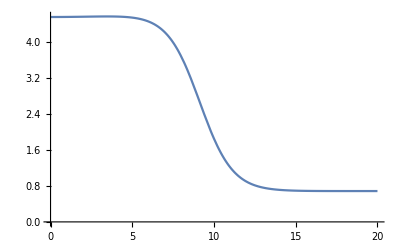

```mathematica
Plot[n[x,T]/.params/.initRun,{x,0,L/.params}]
```

```mathematica
statSol=Block[{n,eta},FindRoot[
fdSetup["Eqs"]/.params,
getInitGuess[fdSetup,params,initRun]
]
];
```

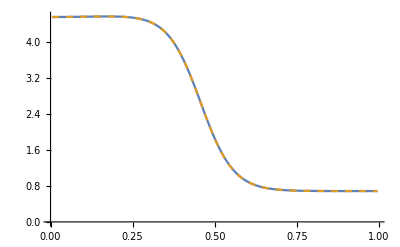

```mathematica
ListLinePlot[{
Transpose[{x,n[L x,T]/.params/.initRun}/.x->fdSetup["UnitGrid"]],
Transpose[{fdSetup["UnitGrid"],fdSetup["nVec"]/.statSol}]
},
PlotRange->All,
PlotStyle->{Default,Dashed}
]
```

## D_v-ϵ-sweep

The stationary state for the Brusselator model is not independent of D_v, has to be calculated separately for each D_v.

### Sweep for numerical LSA

```mathematica
DvEpsSweep[L->20]=Monitor[
Block[{
paramsL,
iniSol,iniSolTemp,discSol,sol,
jac,eval,evalS
},
Table[(*Dv sweep*)(*eps sweep*)
paramsL=Join[{Dv->DvIter,eps->epsIter},fixedParams];
If[epsIter < 10^-6,(*otherwise convergence to slow*)
iniSolTemp=Quiet[runTwoComponentSim[
fTot,
Join[{Dv->DvIter,eps->10^-6},fixedParams],
{
Interpolation[Transpose@{fdSetup["UnitGrid"]*L/.params,fdSetup["nVec"]/.statSol}],
Interpolation[Transpose@{fdSetup["UnitGrid"]*L/.params,fdSetup["etaVec"]/.statSol}]
},
T/.fixedParams
],InterpolatingFunction::dmval];
iniSol=runTwoComponentSim[
fTot,
paramsL,
{
(n[#,T/.paramsL]/.iniSolTemp)&,
(eta[#,T/.paramsL]/.iniSolTemp)&
},
T/.fixedParams
];,
iniSol=Quiet[runTwoComponentSim[
fTot,
paramsL,
{
Interpolation[Transpose@{fdSetup["UnitGrid"]*L/.params,fdSetup["nVec"]/.statSol}],
Interpolation[Transpose@{fdSetup["UnitGrid"]*L/.params,fdSetup["etaVec"]/.statSol}]
},
T/.fixedParams
],InterpolatingFunction::dmval];
];

discSol=n[x*L,T]/.paramsL/.iniSol/.x->Range[0.02,1,0.04];
(*test for pattern being uniform*)
If[Variance[discSol]<10^-2,
PrintTemporary["No pattern!"];
{
{DvIter,epsIter},
 I,
I
},
(*test for pattern having two peaks, first condition tests whether the mesa separated from the boundary x=0 (splitting of upper plateau),
second condition tests for splitting of lower plateau*)
If[(discSol[[1]]<Max[discSol]/2 ||Length@Select[FindPeaks[discSol],#[[2]]>Max[discSol]/2&]>1),
PrintTemporary["Peak splitted!"];
{
{DvIter,epsIter},
 2I,
2I
},
sol=Quiet[Check[Block[{n,eta},FindRoot[
fdSetup["Eqs"]/.paramsL,
getInitGuess[fdSetup,paramsL,iniSol],AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->100,MaxIterations->20]],3I,FindRoot::cvmit],FindRoot::cvmit];
If[sol===3I,
PrintTemporary["Not converging!"];
{
{DvIter,epsIter},
3I,
3I
},
jac=SetPrecision[Normal@constructGluedJacobian[
fdSetup,
paramsL,
sol,
D[{eps (fTot[[2]]+fTot[[3]]),-fTot[[1]]+eps (Du/Dv*fTot[[2]]+fTot[[3]])},{{n,η}}],
"Reverse"->False
],MachinePrecision];
eval=Max[Re@Eigenvalues[jac]];
jac=SetPrecision[Normal@constructGluedJacobian[
fdSetup,
paramsL,
sol,
D[{eps (fTot[[2]]+fTot[[3]]),-fTot[[1]]+eps (Du/Dv*fTot[[2]]+fTot[[3]])},{{n,η}}],
"Reverse"->False,
"Symmetric"->True
],MachinePrecision];
evalS=SortBy[SortBy[Eigenvalues[jac],Re[#]&][[-2;;]],Abs[Re@#]&][[-1]];
If[epsIter>10^-2||epsIter<10^-6,
{
{DvIter,epsIter},
eval,
evalS,
sol
},
{
{DvIter,epsIter},
eval,
evalS
}
]]]],{DvIter,10^Range[4/10,6,2/10]},{epsIter,10^Range[-9,2/10,2/10]}
]],
N@{Log10@epsIter,Log10@DvIter,
Plot[n[x*L,T]/.paramsL/.iniSol,{x,0,1}],
ListPlot[Transpose@{fdSetup["UnitGrid"],Re[fdSetup["nVec"]/.sol]},PlotRange->All]}
];//AbsoluteTiming
```

{1667.74,Null}

### For the growth-rate formulas, a finer separate Dv sweep:

```mathematica
fdSetupMC=setupFiniteDifferenceEqsMC[f,200];
```

```mathematica
analytThresholds=Monitor[Block[{aRes},
First@Last@Reap@Do[
aRes=analytics[fTot,Join[{Dv->DvIter,eps->10^-3},fixedParams],fdSetupMC];
If[aRes["failed"],,Sow@aRes],
{DvIter,10^Join[Range[2/10,6,5/100]]}]
],
{N[DvIter],
Plot[n[x*L,35*t0]/.params/.initRun,{x,0,1}],
ListPlot[{Transpose@{fdSetupMC["UnitGrid"],fdSetupMC["nVec"]/.statSol1}}]
}];//AbsoluteTiming
```

{206.969,Null}

### Stability regions

#### Analytic approximations in the mesa- and peak-forming regimes

analytic formula for mesas in the Brusselator

```mathematica
epsStopM=(6 √Du)/((1-√(Du/(2Dv))p)^2 L)Exp[-2L p/(√(2Dv))];
```

analytic formula for peak regime

```mathematica
epsStopP=24/(((2L)^3 p^2)/(√Du Dv)-20);
```

#### Plot

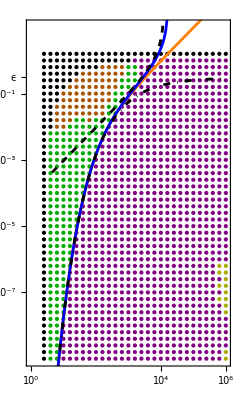

```mathematica
Graphics[{
(*single-domain instability, non-oscillatory*)
Darker@Red,
Point[Log10@Select[Flatten[DvEpsSweep[L->20],1],Re[#[[2]]]<Re[#[[3]]]&&Im[#[[3]]]==0&&Re[#[[3]]]>0&][[All,1]]],
(*single-domain instability, oscillatory*)
Darker@Blue,
Point[Log10@Select[Flatten[DvEpsSweep[L->20],1],Re[#[[2]]]<Re[#[[3]]]&&Im[#[[3]]]≠0&&Re[#[[3]]]>0&][[All,1]]],
(*mass-competition instability*)
Purple,
Point[Log10@Select[Flatten[DvEpsSweep[L->20],1],Re[#[[2]]]>Re[#[[3]]]&&Im[#[[2]]]==0&&Re[#[[2]]]>0&][[All,1]]],
(*two-domain instability, oscillatory*)
Pink,
Point[Log10@Select[Flatten[DvEpsSweep[L->20],1],Length[#]>2&&Re[#[[2]]]>Re[#[[3]]]&&Im[#[[2]]]≠0&&Re[#[[2]]]>0&][[All,1]]],
(*stable*)
Darker@Green,
Point[Log10@Select[Flatten[DvEpsSweep[L->20],1],Re[#[[3]]]<0&&Re[#[[2]]]<0&][[All,1]]],
(*NDSolve peak splitting*)
Darker@Orange,
Point[Log10@Select[Flatten[DvEpsSweep[L->20],1],Im[#[[2]]]==2&&Re[#[[2]]]==0&][[All,1]]],
(*FindRoot not converging*)
Darker@Yellow,
Point[Log10@Select[Flatten[DvEpsSweep[L->20],1],Im[#[[2]]]==3&&Re[#[[2]]]==0&][[All,1]]],
(*NDSolve uniform*)
Black,
Point[Log10@Select[Flatten[DvEpsSweep[L->20],1],Im[#[[2]]]==1&&Re[#[[2]]]==0&][[All,1]]],


AbsoluteThickness[2],
(*epsCrit diff. limit of Eq. (H8)*)
Orange,
Line[{Log10[Dv/.#["params"]],Log10[-#["sigmaD"]/(#["<sRhoRho>"]+(√(Du/(2Dv))p/(1-Du/Dv)/.#["params"]))]}&/@analytThresholds],
(*full epsStop, Eq. (H8)*)
Blue,
Line[Select[{Log10[Dv/.#["params"]],Log10[#["epsStop"]]}&/@analytThresholds,Im[#[[2]]]==0&]],
(*analytic mesa epsStop, Eq. (47)*)
Black,DotDashed,
Line[{Log10[Dv],Log10[epsStopM]}/.#["params"]&/@analytThresholds],
(*analytic scaling peaks epsStop, Eq. (48)*)
Black,Dashed,
Line[Select[{Log10[Dv],Log10[epsStopP]}/.#["params"]&/@analytThresholds,Im[#[[2]]]==0&]]
},
PlotRange->{{-0.02,6.02},{-9.02,1.02}},PlotRangeClipping->True,
Frame->True,
BaseStyle->14,FrameStyle->Black,
FrameTicks->{{
{{-7,"10^-7",{0,0.02}},{-5,"10^-5",{0,0.02}},{-3,"10^-3",{0,0.02}},{-0.5,"ϵ  ",{0,0}},{-1,"10^-1",{0,0.02}}},
None
},{
{{0,"10^0",{0,0.02}},{2,"10^2",{0,0.02}},{4,"10^4",{0,0.02}},{5.5,"Dv",{0,0}},{6,"10^6",{0,0.02}}},
None
}
}
]
```

### Growth rates

#### σ(D_v) at ϵ=10^-1

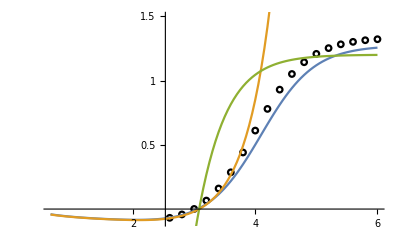

```mathematica
logEps=1;
ind=First@First@Position[N[DvEpsSweep[L->20][[1,All,1,2]]],x_/;Abs[x-10^-logEps]<10^-7];
Show[
ListPlot[
{{Log10@#[[1,1]],#[[2]]}&/@DvEpsSweep[L->20][[All,ind]]},
PlotRange->All,PlotMarkers->{Graphics[{Black,Circle[]}],0.04}
],
ListLinePlot[{{Log10@Dv/.#["params"],#["sigma"]/.eps->10^-logEps}&/@analytThresholds,
{Log10@Dv/.#["params"],(σD-eps Abs@(#["<sRhoRho>"]+(√(Du/(2Dv))p/(1-Du/Dv)/.#["params"])))/.eps->10^-logEps/.{σD->#["sigmaD"],σR->#["sigmaR"]}}&/@analytThresholds,
{Log10@Dv/.#["params"],(1-eps Abs@(#["<sRhoRho>"]+(√(Du/(2Dv))p/(1-Du/Dv)/.#["params"]))/σD)/(1/σR)/.eps->10^-logEps/.{σD->#["sigmaD"],σR->#["sigmaR"]}}&/@analytThresholds}],
PlotRange->{-10^-1,1.5*10^-0},
PlotLegends->{
"finite differences eigenvalues",
"σ",
"σ_McKay",
"σ_diffLimit",
"σ_inclWrongTerm"
},
Ticks->{{0,2,4,6},{0.5,1,1.5}}
]
```

#### σ(D_v) at ϵ=10^-5

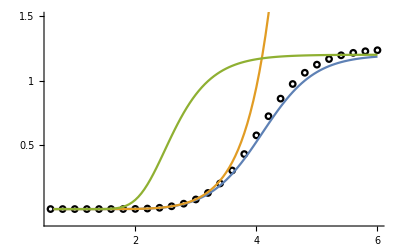

```mathematica
logEps=5;
ind=First@First@Position[N[DvEpsSweep[L->20][[1,All,1,2]]],x_/;Abs[x-10^-logEps]<10^-7];
Show[
ListPlot[
{Log10@#[[1,1]],#[[2]]}&/@DvEpsSweep[L->20][[All,ind]],
PlotRange->All,PlotMarkers->{Graphics[{Black,Circle[]}],0.04}
],
ListLinePlot[{{Log10@Dv/.#["params"],#["sigma"]/.eps->10^-logEps}&/@analytThresholds,
{Log10@Dv/.#["params"],(σD-eps Abs@(#["<sRhoRho>"]+(√(Du/(2Dv))p/(1-Du/Dv)/.#["params"])))/.eps->10^-logEps/.{σD->#["sigmaD"],σR->#["sigmaR"]}}&/@analytThresholds,
{Log10@Dv/.#["params"],(1-eps Abs@(#["<sRhoRho>"]+(√(Du/(2Dv))p/(1-Du/Dv)/.#["params"]))/σD)/(1/σR)/.eps->10^-logEps/.{σD->#["sigmaD"],σR->#["sigmaR"]}}&/@analytThresholds}],
PlotRange->{-1*10^-1,1.5*10^-0},
PlotLegends->{
"finite differences eigenvalues",
"σ",
"σ_McKay",
"σ_diffLimit",
"σ_inclWrongTerm"
},
Ticks->{{0,2,4,6},{0.5,1,1.5}}
]
```

## Source terms (s_1,s_2)=(0,p-u)

### Model setup

Brusselator (mass-conserving part) reaction kinetics in (n,η) variables

```mathematica
f=(1-Du/Dv)(u^2*v-u)/.{u->((n-η)/(1-Du/Dv)),v->((η-Du/Dv*n)/(1-Du/Dv))};(*\tilde{f}*)
source=p-u/.u->((n-η)/(1-Du/Dv));
fTot={f,0,source};
```

```mathematica
fixedParams={p->2,Du->1,L->20,T->10^8};
params=Join[{eps->10^-3,Dv->10},fixedParams];
```

```mathematica
fdSetup=setupFiniteDifferenceEqs[fTot,100];
```

## Stationary state for initialization

```mathematica
initRun=runTwoComponentSim[
fTot,
params,
{
2+0.5Cos[Pi#/L]&,
0&
},
T/.fixedParams
];
```

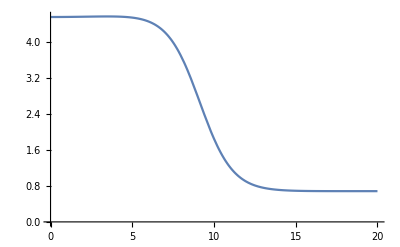

```mathematica
Plot[n[x,T]/.params/.initRun,{x,0,L/.params}]
```

```mathematica
statSol=Block[{n,eta},FindRoot[
fdSetup["Eqs"]/.params,
getInitGuess[fdSetup,params,initRun]
]
];
```

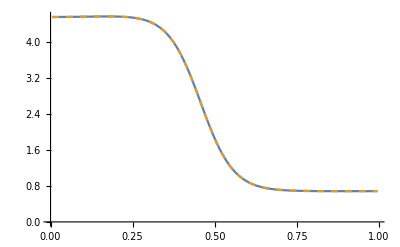

```mathematica
ListLinePlot[{
Transpose[{x,n[L x,T]/.params/.initRun}/.x->fdSetup["UnitGrid"]],
Transpose[{fdSetup["UnitGrid"],fdSetup["nVec"]/.statSol}]
},
PlotRange->All,
PlotStyle->{Default,Dashed}
]
```

## D_v-ϵ-sweep

The stationary state for the Brusselator model is not independent of D_v, has to be calculated separately for each D_v.

### Sweep for numerical LSA

```mathematica
DvEpsSweepV[L->20]=Monitor[
Block[{
paramsL,
iniSol,iniSolTemp,discSol,sol,
jac,eval,evalS
},
Table[(*Dv sweep*)(*eps sweep*)
paramsL=Join[{Dv->DvIter,eps->epsIter},fixedParams];
If[epsIter < 10^-6,(*otherwise convergence to slow*)
iniSolTemp=Quiet[runTwoComponentSim[
fTot,
Join[{Dv->DvIter,eps->10^-6},fixedParams],
{
Interpolation[Transpose@{fdSetup["UnitGrid"]*L/.params,fdSetup["nVec"]/.statSol}],
Interpolation[Transpose@{fdSetup["UnitGrid"]*L/.params,fdSetup["etaVec"]/.statSol}]
},
T/.fixedParams
],InterpolatingFunction::dmval];
iniSol=runTwoComponentSim[
fTot,
paramsL,
{
(n[#,T/.paramsL]/.iniSolTemp)&,
(eta[#,T/.paramsL]/.iniSolTemp)&
},
T/.fixedParams
];,
iniSol=Quiet[runTwoComponentSim[
fTot,
paramsL,
{
Interpolation[Transpose@{fdSetup["UnitGrid"]*L/.params,fdSetup["nVec"]/.statSol}],
Interpolation[Transpose@{fdSetup["UnitGrid"]*L/.params,fdSetup["etaVec"]/.statSol}]
},
T/.fixedParams
],InterpolatingFunction::dmval];
];

discSol=n[x*L,T]/.paramsL/.iniSol/.x->Range[0.02,1,0.04];
(*test for pattern being uniform*)
If[Variance[discSol]<10^-2,
PrintTemporary["No pattern!"];
{
{DvIter,epsIter},
 I,
I
},
(*test for pattern having two peaks, first condition tests whether the mesa separated from the boundary x=0 (splitting of upper plateau),
second condition tests for splitting of lower plateau*)
If[(discSol[[1]]<Max[discSol]/2 ||Length@Select[FindPeaks[discSol],#[[2]]>Max[discSol]/2&]>1),
PrintTemporary["Peak splitted!"];
{
{DvIter,epsIter},
 2I,
2I
},
sol=Quiet[Check[Block[{n,eta},FindRoot[
fdSetup["Eqs"]/.paramsL,
getInitGuess[fdSetup,paramsL,iniSol],AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->100,MaxIterations->20]],3I,FindRoot::cvmit],FindRoot::cvmit];
If[sol===3I,
PrintTemporary["Not converging!"];
{
{DvIter,epsIter},
3I,
3I
},
jac=SetPrecision[Normal@constructGluedJacobian[
fdSetup,
paramsL,
sol,
D[{eps (fTot[[2]]+fTot[[3]]),-fTot[[1]]+eps (Du/Dv*fTot[[2]]+fTot[[3]])},{{n,η}}],
"Reverse"->False
],MachinePrecision];
eval=Max[Re@Eigenvalues[jac]];
jac=SetPrecision[Normal@constructGluedJacobian[
fdSetup,
paramsL,
sol,
D[{eps (fTot[[2]]+fTot[[3]]),-fTot[[1]]+eps (Du/Dv*fTot[[2]]+fTot[[3]])},{{n,η}}],
"Reverse"->False,
"Symmetric"->True
],MachinePrecision];
evalS=SortBy[SortBy[Eigenvalues[jac],Re[#]&][[-2;;]],Abs[Re@#]&][[-1]];
If[epsIter>10^-2||epsIter<10^-6,
{
{DvIter,epsIter},
eval,
evalS,
sol
},
{
{DvIter,epsIter},
eval,
evalS
}
]]]],{DvIter,10^Range[4/10,6,2/10]},{epsIter,10^Range[-9,2/10,2/10]}
]],
N@{Log10@epsIter,Log10@DvIter,
Plot[n[x*L,T]/.paramsL/.iniSol,{x,0,1}],
ListPlot[Transpose@{fdSetup["UnitGrid"],Re[fdSetup["nVec"]/.sol]},PlotRange->All]}
];//AbsoluteTiming
```

{1832.33,Null}

### For the growth-rate formulas, a finer separate Dv sweep:

```mathematica
fdSetupMC=setupFiniteDifferenceEqsMC[f,200];
```

```mathematica
analytThresholds=Monitor[Block[{aRes},
First@Last@Reap@Do[
aRes=analytics[fTot,Join[{Dv->DvIter,eps->10^-3},fixedParams],fdSetupMC];
If[aRes["failed"],,Sow@aRes],
{DvIter,10^Join[Range[2/10,6,5/100]]}]
],
{N[DvIter],
Plot[n[x*L,35*t0]/.params/.initRun,{x,0,1}],
ListPlot[{Transpose@{fdSetupMC["UnitGrid"],fdSetupMC["nVec"]/.statSol1}}]
}];//AbsoluteTiming
```

{490.95,Null}

### Stability regions

#### Analytic approximations in the mesa- and peak-forming regimes

analytic formula for mesas in the Brusselator

```mathematica
epsStopM=(6 √Du)/((1-√(Du/(2Dv))p)^2 L)Exp[-2L p/(√(2Dv))];
```

analytic formula for peak regime

```mathematica
epsStopP=(24 √Du Dv)/((2L)^3 p^2);
```

#### Plot

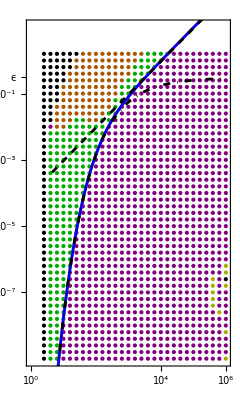

```mathematica
Graphics[{
(*single-domain instability, non-oscillatory*)
Darker@Red,
Point[Log10@Select[Flatten[DvEpsSweepV[L->20],1],Re[#[[2]]]<Re[#[[3]]]&&Im[#[[3]]]==0&&Re[#[[3]]]>0&][[All,1]]],
(*single-domain instability, oscillatory*)
Darker@Blue,
Point[Log10@Select[Flatten[DvEpsSweepV[L->20],1],Re[#[[2]]]<Re[#[[3]]]&&Im[#[[3]]]≠0&&Re[#[[3]]]>0&][[All,1]]],
(*mass-competition instability*)
Purple,
Point[Log10@Select[Flatten[DvEpsSweepV[L->20],1],Re[#[[2]]]>Re[#[[3]]]&&Im[#[[2]]]==0&&Re[#[[2]]]>0&][[All,1]]],
(*two-domain instability, oscillatory*)
Pink,
Point[Log10@Select[Flatten[DvEpsSweepV[L->20],1],Length[#]>2&&Re[#[[2]]]>Re[#[[3]]]&&Im[#[[2]]]≠0&&Re[#[[2]]]>0&][[All,1]]],
(*stable*)
Darker@Green,
Point[Log10@Select[Flatten[DvEpsSweepV[L->20],1],Re[#[[3]]]<0&&Re[#[[2]]]<0&][[All,1]]],
(*NDSolve peak splitting*)
Darker@Orange,
Point[Log10@Select[Flatten[DvEpsSweepV[L->20],1],Im[#[[2]]]==2&&Re[#[[2]]]==0&][[All,1]]],
(*FindRoot not converging*)
Darker@Yellow,
Point[Log10@Select[Flatten[DvEpsSweepV[L->20],1],Im[#[[2]]]==3&&Re[#[[2]]]==0&][[All,1]]],
(*NDSolve uniform*)
Black,
Point[Log10@Select[Flatten[DvEpsSweepV[L->20],1],Im[#[[2]]]==1&&Re[#[[2]]]==0&][[All,1]]],


AbsoluteThickness[2],
(*epsCrit diff. limit of Eq. (H8)*)
Orange,
Line[{Log10[Dv/.#["params"]],Log10[-#["sigmaD"]/(#["<sRhoRho>"]+(√(Du/(2Dv))p/(1-Du/Dv)/.#["params"]))]}&/@analytThresholds],
(*full epsStop, Eq. (H8)*)
Blue,
Line[Select[{Log10[Dv/.#["params"]],Log10[#["epsStop"]]}&/@analytThresholds,Im[#[[2]]]==0&]],
(*analytic mesa epsStop, Eq. (47)*)
Black,DotDashed,
Line[{Log10[Dv],Log10[epsStopM]}/.#["params"]&/@analytThresholds],
(*analytic scaling peaks epsStop, Eq. (48)*)
Black,Dashed,
Line[Select[{Log10[Dv],Log10[epsStopP]}/.#["params"]&/@analytThresholds,Im[#[[2]]]==0&]]
},
PlotRange->{{-0.02,6.02},{-9.02,1.02}},PlotRangeClipping->True,
Frame->True,
BaseStyle->14,FrameStyle->Black,
FrameTicks->{{
{{-7,"10^-7",{0,0.02}},{-5,"10^-5",{0,0.02}},{-3,"10^-3",{0,0.02}},{-0.5,"ϵ  ",{0,0}},{-1,"10^-1",{0,0.02}}},
None
},{
{{0,"10^0",{0,0.02}},{2,"10^2",{0,0.02}},{4,"10^4",{0,0.02}},{5.5,"Dv",{0,0}},{6,"10^6",{0,0.02}}},
None
}
}
]
```

### Profiles

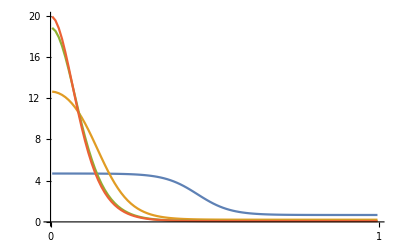

```mathematica
ListLinePlot[Transpose[{fdSetup["UnitGrid"],fdSetup["nVec"]/.#}]&/@DvEpsSweepV[L->20][[{4,9,14,19},1,-1]],
PlotRange->All,
Ticks->{{0,1},None}]
```

### Growth rates

#### σ(D_v) at ϵ=10^-1

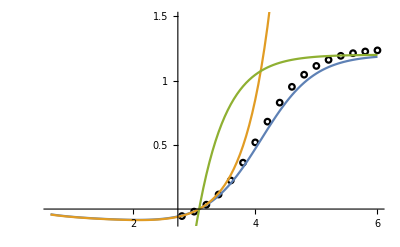

```mathematica
logEps=1;
ind=First@First@Position[N[DvEpsSweepV[L->20][[1,All,1,2]]],x_/;Abs[x-10^-logEps]<10^-7];
Show[
ListPlot[
{{Log10@#[[1,1]],#[[2]]}&/@DvEpsSweepV[L->20][[All,ind]]},
PlotRange->All,PlotMarkers->{Graphics[{Black,Circle[]}],0.04}
],
ListLinePlot[{{Log10@Dv/.#["params"],#["sigma"]/.eps->10^-logEps}&/@analytThresholds,
{Log10@Dv/.#["params"],(σD-eps Abs@(#["<sRhoRho>"]+(√(Du/(2Dv))p/(1-Du/Dv)/.#["params"])))/.eps->10^-logEps/.{σD->#["sigmaD"],σR->#["sigmaR"]}}&/@analytThresholds,
{Log10@Dv/.#["params"],(1-eps Abs@(#["<sRhoRho>"]+(√(Du/(2Dv))p/(1-Du/Dv)/.#["params"]))/σD)/(1/σR)/.eps->10^-logEps/.{σD->#["sigmaD"],σR->#["sigmaR"]}}&/@analytThresholds}],
PlotRange->{-10^-1,1.5*10^-0},
PlotLegends->{
"finite differences eigenvalues",
"σ",
"σ_McKay",
"σ_diffLimit",
"σ_inclWrongTerm"
},
Ticks->{{0,2,4,6},{0.5,1,1.5}}
]
```

#### σ(D_v) at ϵ=10^-3

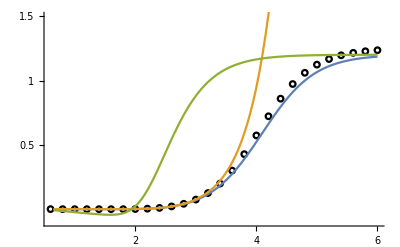

```mathematica
logEps=3;
ind=First@First@Position[N[DvEpsSweepV[L->20][[1,All,1,2]]],x_/;Abs[x-10^-logEps]<10^-7];
Show[
ListPlot[
{{Log10@#[[1,1]],#[[2]]}&/@DvEpsSweepV[L->20][[All,ind]]},
PlotRange->All,PlotMarkers->{Graphics[{Black,Circle[]}],0.04}
],
ListLinePlot[{{Log10@Dv/.#["params"],#["sigma"]/.eps->10^-logEps}&/@analytThresholds,
{Log10@Dv/.#["params"],(σD-eps Abs@(#["<sRhoRho>"]+(√(Du/(2Dv))p/(1-Du/Dv)/.#["params"])))/.eps->10^-logEps/.{σD->#["sigmaD"],σR->#["sigmaR"]}}&/@analytThresholds,
{Log10@Dv/.#["params"],(1-eps Abs@(#["<sRhoRho>"]+(√(Du/(2Dv))p/(1-Du/Dv)/.#["params"]))/σD)/(1/σR)/.eps->10^-logEps/.{σD->#["sigmaD"],σR->#["sigmaR"]}}&/@analytThresholds}],
PlotRange->{-1*10^-1,1.5*10^-0},
PlotLegends->{
"finite differences eigenvalues",
"σ",
"σ_McKay",
"σ_diffLimit",
"σ_inclWrongTerm"
},
Ticks->{{0,2,4,6},{0.5,1,1.5}}
]
```

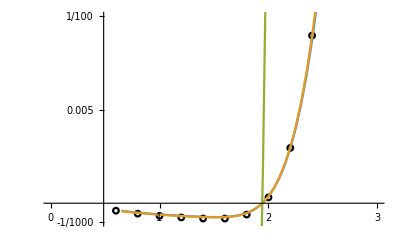

```mathematica
logEps=3;
ind=First@First@Position[N[DvEpsSweepV[L->20][[1,All,1,2]]],x_/;Abs[x-10^-logEps]<10^-7];
Show[
ListPlot[
{{Log10@#[[1,1]],#[[2]]}&/@DvEpsSweepV[L->20][[All,ind]]},
PlotRange->All,PlotMarkers->{Graphics[{Black,Circle[]}],0.04}
],
ListLinePlot[{{Log10@Dv/.#["params"],#["sigma"]/.eps->10^-logEps}&/@analytThresholds,
{Log10@Dv/.#["params"],(σD-eps Abs@(#["<sRhoRho>"]+(√(Du/(2Dv))p/(1-Du/Dv)/.#["params"])))/.eps->10^-logEps/.{σD->#["sigmaD"],σR->#["sigmaR"]}}&/@analytThresholds,
{Log10@Dv/.#["params"],(1-eps Abs@(#["<sRhoRho>"]+(√(Du/(2Dv))p/(1-Du/Dv)/.#["params"]))/σD)/(1/σR)/.eps->10^-logEps/.{σD->#["sigmaD"],σR->#["sigmaR"]}}&/@analytThresholds}],
PlotRange->{{0,3},{-1*10^-3,1*10^-2}},
PlotLegends->{
"finite differences eigenvalues",
"σ",
"σ_McKay",
"σ_diffLimit",
"σ_inclWrongTerm"
},
Ticks->{{0,1,2,3},{-10^-3,0.5*10^-2,10^-2}}
]
```

#### σ(D_v) at ϵ=10^-5

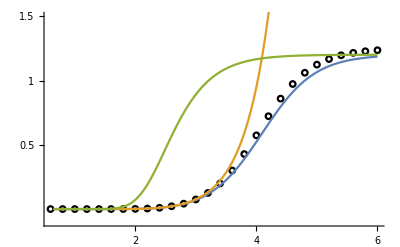

```mathematica
logEps=5;
ind=First@First@Position[N[DvEpsSweepV[L->20][[1,All,1,2]]],x_/;Abs[x-10^-logEps]<10^-7];
Show[
ListPlot[
{Log10@#[[1,1]],#[[2]]}&/@DvEpsSweepV[L->20][[All,ind]],
PlotRange->All,PlotMarkers->{Graphics[{Black,Circle[]}],0.04}
],
ListLinePlot[{{Log10@Dv/.#["params"],#["sigma"]/.eps->10^-logEps}&/@analytThresholds,
{Log10@Dv/.#["params"],(σD-eps Abs@(#["<sRhoRho>"]+(√(Du/(2Dv))p/(1-Du/Dv)/.#["params"])))/.eps->10^-logEps/.{σD->#["sigmaD"],σR->#["sigmaR"]}}&/@analytThresholds,
{Log10@Dv/.#["params"],(1-eps Abs@(#["<sRhoRho>"]+(√(Du/(2Dv))p/(1-Du/Dv)/.#["params"]))/σD)/(1/σR)/.eps->10^-logEps/.{σD->#["sigmaD"],σR->#["sigmaR"]}}&/@analytThresholds}],
PlotRange->{-1*10^-1,1.5*10^-0},
PlotLegends->{
"finite differences eigenvalues",
"σ",
"σ_McKay",
"σ_diffLimit",
"σ_inclWrongTerm"
},
Ticks->{{0,2,4,6},{0.5,1,1.5}}
]
```

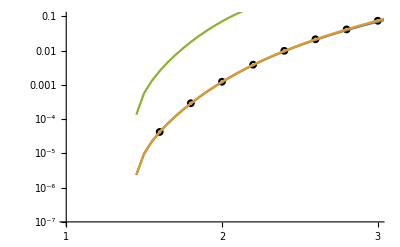

```mathematica
logEps=5;
ind=First@First@Position[N[DvEpsSweepV[L->20][[1,All,1,2]]],x_/;Abs[x-10^-logEps]<10^-7];
Show[
ListLogPlot[
{{Log10@#[[1,1]],#[[2]]}&/@DvEpsSweepV[L->20][[All,ind]]},
PlotMarkers->{Graphics[{Black,Circle[]}],0.04},
PlotRange->{{1,3},{10^-7,1*10^-1}},
Ticks->{{1,2,3},{10^-5,10^-3,10^-1}}
],
ListLogPlot[{{Log10@Dv/.#["params"],#["sigma"]/.eps->10^-logEps}&/@analytThresholds,
{Log10@Dv/.#["params"],(σD-eps Abs@(#["<sRhoRho>"]+(√(Du/(2Dv))p/(1-Du/Dv)/.#["params"])))/.eps->10^-logEps/.{σD->#["sigmaD"],σR->#["sigmaR"]}}&/@analytThresholds,
{Log10@Dv/.#["params"],(1-eps Abs@(#["<sRhoRho>"]+(√(Du/(2Dv))p/(1-Du/Dv)/.#["params"]))/σD)/(1/σR)/.eps->10^-logEps/.{σD->#["sigmaD"],σR->#["sigmaR"]}}&/@analytThresholds},
Joined->True],
PlotLegends->{
"finite differences eigenvalues",
"σ",
"σ_McKay",
"σ_diffLimit",
"σ_inclWrongTerm"
}
]
```